## Kapitola 13 - Shlukování dat sítí bez učitele

Demonstrace použití neuronové sítě bez učitele k hledání shluků v datech.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Vytvoření trénovacích dat

Vygenerujeme si data, na kterých budeme prezentovat shlukování. Protože pracujeme se sítí bez učitele, postačí nám vstupní data a nepotřebujeme generovat žádná výstupní data.

```mathematica
values=10;
(* hodnoty ve {,} udávají x-ový a y-ový rozsah každého shluku *)
cluster1x =RandomReal[{-0.1,0.1},{values,1}];cluster1y=RandomReal[ {-0.1,0.1},{values,1}];
cluster2x =RandomReal[{-0.1,0.1},{values,1}];cluster2y=RandomReal[ {0.9,1.1},{values,1}];
cluster3x =RandomReal[{0.3,0.5},{values,1}];cluster3y=RandomReal[ {1.4,1.6},{values,1}];
cluster4x =RandomReal[{0.9,1.1},{values,1}];cluster4y=RandomReal[ {2.1,1.9},{values,1}];
cluster5x =RandomReal[{1.4,1.6},{values,1}];cluster5y=RandomReal[ {1.4,1.6},{values,1}];
cluster6x =RandomReal[{1.9,2.1},{values,1}];cluster6y=RandomReal[ {1.1,0.9},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inData= Join[cluster1,cluster2,cluster3,cluster4,cluster5,cluster6];
```

Vygenerovaná data jsou dvoudimenzionální a obsahují 6 jasně oddělených shluků.

Data si můžeme zobrazit zde.

```mathematica
inData
```

{{-0.0547808,-0.0456178},{0.0304682,-0.0490266},{0.0172445,0.058694},{0.0482627,0.0420679},{0.0614994,-0.0928119},{0.034417,0.0117083},{0.0219176,-0.0594172},{0.0765806,-0.0712351},{-0.0177977,0.0529227},{0.0163712,-0.0519516},{0.031009,0.958986},{0.00158998,1.004},{-0.0977732,0.914437},{0.0228203,1.05502},{-0.0218662,1.0493},{0.0641962,1.08636},{0.0831697,1.01807},{0.0617175,0.901713},{0.0392356,0.917852},{-0.0427919,1.05376},{0.427558,1.47363},{0.379727,1.40365},{0.469602,1.48858},{0.395236,1.40183},{0.334256,1.5774},{0.336206,1.58804},{0.444234,1.57365},{0.428754,1.42096},{0.311492,1.43523},{0.461752,1.54166},{1.01559,1.90199},{1.08006,2.04914},{1.07442,1.99404},{0.948119,1.9536},{1.06679,2.01173},{0.940703,2.09652},{1.0342,2.06185},{0.969056,2.08887},{0.94018,1.97967},{0.921761,1.99094},{1.44432,1.59392},{1.54463,1.5242},{1.5791,1.59503},{1.46189,1.42442},{1.56722,1.56884},{1.42299,1.51202},{1.42479,1.4961},{1.44369,1.40091},{1.59055,1.49425},{1.46238,1.51606},{2.07591,1.01257},{1.952,1.01112},{1.91174,1.06473},{2.08857,1.03328},{1.94645,0.954736},{2.02431,0.955656},{2.0391,1.08338},{2.01281,0.974823},{2.06022,0.978638},{1.9998,1.04328}}

Pro lepší představu o struktuře dat si je můžeme zobrazit v grafu.

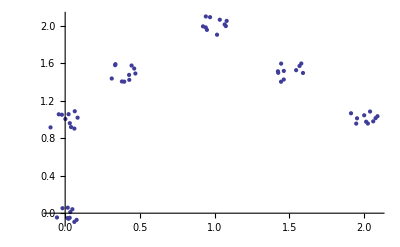

```mathematica
ListPlot[inData]
```

## Zpracování dat neuronovou sítí

Samoorganizující se neuronovou síť použijeme k hledání shluků ve vygenerovaných datech. Vytvoříme síť o šesti neuronech, kterou necháme na datech naučit. Po naučení sítě chceme aby ideálně každý neuron reprezentoval jeden shluk ve vstupních datech. Poté je možné spočítat hraniční přímky mezi jednotlivými neurony a tím de facto rozdělit do požadovaného počtu shluků celý vstupní prostor.

### Náhodně inicializovaná síť

Nejprve vytvoříme neuronovou síť o šesti neuronech. Počet neuronů určuje kolik shluků se síť pokusí v datech najít.

```mathematica
unsup=InitializeUnsupervisedNet[inData,6];
```

Tuto neuronovou síť naučíme na našich datech

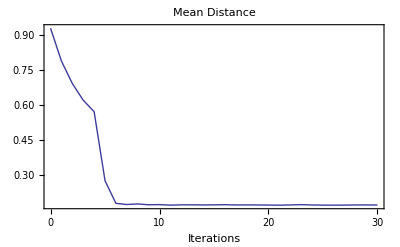

UnsupervisedNet::DeadNeuron: Some codebook vectors are not used by the data. They have 'died' during the training. Use UnUsedNeurons to identify them and decide if you want to remove them.

```mathematica
{unsup,fitrecord}=UnsupervisedNetFit[inData,unsup,30,ReportFrequency->1];
```

Vidíme že během učení sítě jeden z neuronů “zemřel”, tzn. není použit k rozlišení shluků v datech. Později se mu ještě budeme věnovat.

Ilustraci jaým způsobem byla data rozdělena do shluků nám poskytne následující graf. Pozice neuronu, který reprezentuje daný shluk je naznačena tučným číslem. Je také jasně vidět, který neuron je “mrtvý” a nepřináší nám žádný užitek.

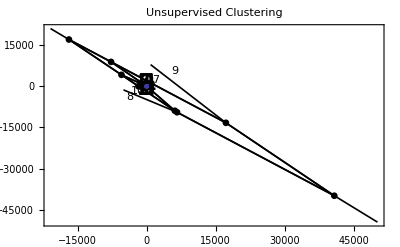

```mathematica
NetPlot[unsup,inData,CbvSymbol->{FontSize->30}]
```

Můžeme také jednoduše nechat “oklasifikovat” nový vektor (zadáme jeho x a y souřadnici).

```mathematica
unsup[{0.2,0.7}]
```

{1}

Číslo, které nám síť vrátila znamená číselné označení shluku, kam vektor spadá (odpovídá číslům v grafu)

Nyní si vzpomeneme, že máme v síti nepotřebný neuron, budeme ho tedy chtít odstranit.
Nejdříve zjistíme o který neuron se jedná.

```mathematica
UnUsedNeurons[unsup,inData]
```

{6}

A poté ho odstraníme. Novou síť bez nepotřebného neuronu pojmenujeme unsup1.

```mathematica
unsup1=NeuronDelete[unsup,%]
```

UnsupervisedNet[{-Codebook Vectors-},{CreationDate → {2011, 5, 23, 0, 47, 20.2530116}, AccumulatedIterations → 30, SOM → None}]

Podíváme se jakým způsobem odděluje síť jednotlivé shluky po odebrání nepotřebného neuronu.

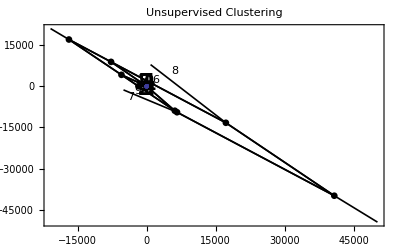

```mathematica
NetPlot[unsup1,inData,CbvSymbol->{FontSize->30}]
```

### Síť inicializovaná metodou SOM

Protože vidíme, že rozdělení dat na shluky ještě není perfektní můžeme se pokust dosáhnout ještě lepšího rozdělení. Místo náhodné inicializace sítě můžeme použít SOM (samoorganizující mapu) k inicializaci sítě. Samoorganizující mapa se nechá přizpůsobit datům, na souřadnicích, kde skončí její neurony, jsou inicializovány neurony naší požadované sítě (naše síť není SOM).

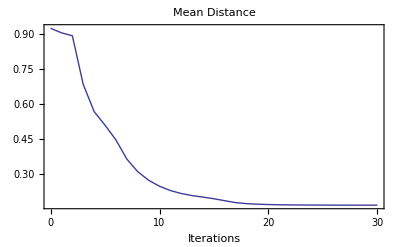

```mathematica
unsup2=InitializeUnsupervisedNet[inData,6,UseSOM ->True,CriterionPlot->True,CriterionLog->True,Iterations->30];
```

Nyní naučíme zinicializovanou síť na našich datech.

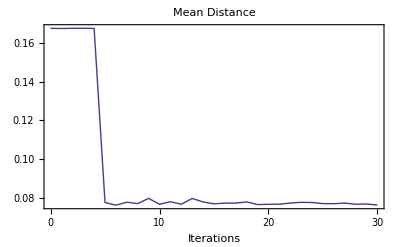

```mathematica
{unsup2,fitrecord2}=UnsupervisedNetFit[inData,unsup2,30];
```

A podíváme se jakým způsobem uřčuje shluky v datech.

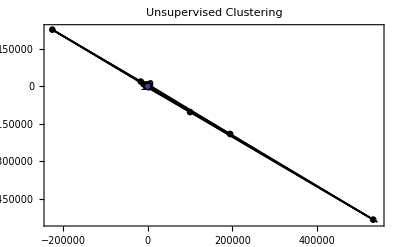

```mathematica
NetPlot[unsup2,inData]
```

Tento přístup k inicializaci sítě nám může často pomoci dosáhnout lepších výsledků, než náhodná inicializace. Také často zabrání problému s “mrtvými” neurony.

## Průběh učení

### Náhodně inicializovaná síť

Ještě se můžeme podívat jak síť v průběhu učení dělila data do shluků a jak se měnila poloha jednotlivých neuronů. Barevné čáry ukazují pohyb jednotlivých neuronů v průběhu učení, čísla ukazují jejich konečnou polohu.

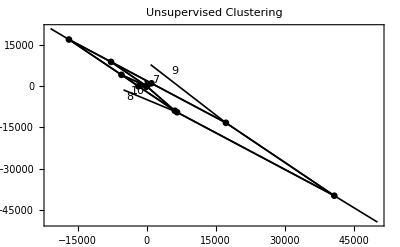

```mathematica
NetPlot[fitrecord,inData]
```

Zde si můžete zobrazit průběh učení po jednotlivých iteracích. Pro správnou funkci je třeba mít vyhodnocené všechny výše se nacházející buňky.

```mathematica
learningState=NetPlot[fitrecord,inData,DataFormat->DataMapArray,Intervals->1][[1,2,All,1,1]];
Manipulate[learningState[[a]],{{a,1, "Iteration"}, 1, 31,1}]
```

### Síť inicializovaná metodou SOM

Z následujícího grafu je patrné, že síť zinicializovaná metodou SOM by poskytovala poměrně dobré výsledky bez nutnosti dalšího učení. Učení upravuje pouze pozici několika neuronů.

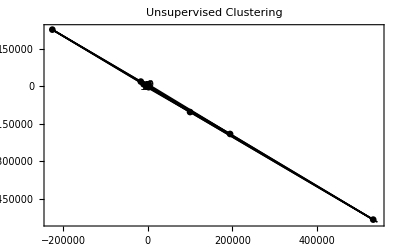

```mathematica
NetPlot[fitrecord2,inData]
```

Zde si můžete zobrazit průběh učení po jednotlivých iteracích. Pro správnou funkci je třeba mít vyhodnocené všechny výše se nacházející buňky.

```mathematica
learningState2=NetPlot[fitrecord2,inData,DataFormat->DataMapArray,Intervals->1][[1,2,All,1,1]];
Manipulate[learningState2[[a]],{{a,1, "Iteration"}, 1, 31,1}]
```

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011.